```mathematica
Clear[x]
Clear[y]
Clear[r]
Clear[h]
Clear[d]
Clear[b]
Clear[px]
Clear[ra]
Clear[rb]
rules=FullSimplify[Solve[{px^2/ra^2+b^2/(4 rb^2)==1,(-r+h/2-b)px/ra^2 +(px*b)/(2 rb^2)==0},{ra,rb}]]
```

{{ra→-1/2 √(4 px^2+b (2 b-h+2 r)),rb→-(ⅈ √b √(4 px^2+b (2 b-h+2 r)))/(2 √(-2 b+h-2 r))},{ra→1/2 √(4 px^2+b (2 b-h+2 r)),rb→-(ⅈ √b √(4 px^2+b (2 b-h+2 r)))/(2 √(-2 b+h-2 r))},{ra→-1/2 √(4 px^2+b (2 b-h+2 r)),rb→(ⅈ √b √(4 px^2+b (2 b-h+2 r)))/(2 √(-2 b+h-2 r))},{ra→1/2 √(4 px^2+b (2 b-h+2 r)),rb→(ⅈ √b √(4 px^2+b (2 b-h+2 r)))/(2 √(-2 b+h-2 r))}}

```mathematica
getRA[px_,b_,h_,r_]:= ra/.rules[[4]]
getRB[px_,b_,h_,r_]:=rb/.rules[[4]]
```

ArcTan[px,b/2]

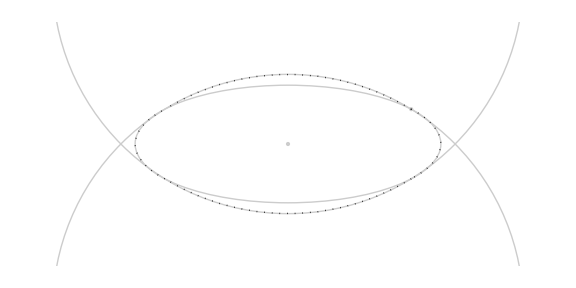

```mathematica
ArcTan[px,b/2]
w=0.18;
h=0.075;
r=(w*w+h*h)/4/h;
b = h/2;
d = r-h/2;
y=b/2+d;
px=√(r*r-y*y);
ra = getRA[px,b,h, r];
rb = getRB[px, b,h,r];
atl = ArcTan[-px,r-h/2+b/2];
atr= ArcTan[px,r-h/2+b/2];
abl = ArcTan[-px,-r+h/2-b/2];
abr = ArcTan[px,-r+h/2-b/2];
btr=ArcTan[px,b/2];
bbr = ArcTan[px,-b/2];
bbl = ArcTan[-px,-b/2];
btl = ArcTan[-px,b/2];
Graphics[{GrayLevel[0.8],Circle[{0,-r+h/2},r],Circle[{0,r-h/2},r],Circle[{0,0},{ra,rb}],Point[{px,b/2}],Point[{0,0}],
Black,
Thick,Dotted,
Circle[{0,-r+h/2},r,{atr,atl}],
Circle[{0,r-h/2},r,{abr,abl}],
Circle[{0,0},{ra,rb},{ArcCos[px/ra],-ArcCos[px/ra]}],
Circle[{0,0},{ra,rb},Pi+{ArcCos[px/ra],-ArcCos[px/ra]}]
},PlotRange->{{-r,r},{-r/2,r/2}},
ImageSize->Large]
```

```mathematica
Solve[(ox+t dx)^2/ra^2+(oy+t dy)^2/rb^2+(oz+t dz)^2/rc^2==1,t]
```

{{t→(-2 dz oz ra^2 rb^2-2 dy oy ra^2 rc^2-2 dx ox rb^2 rc^2-√((2 dz oz ra^2 rb^2+2 dy oy ra^2 rc^2+2 dx ox rb^2 rc^2)^2-4 (dz^2 ra^2 rb^2+dy^2 ra^2 rc^2+dx^2 rb^2 rc^2) (oz^2 ra^2 rb^2+oy^2 ra^2 rc^2+ox^2 rb^2 rc^2-ra^2 rb^2 rc^2)))/(2 (dz^2 ra^2 rb^2+dy^2 ra^2 rc^2+dx^2 rb^2 rc^2))},{t→(-2 dz oz ra^2 rb^2-2 dy oy ra^2 rc^2-2 dx ox rb^2 rc^2+√((2 dz oz ra^2 rb^2+2 dy oy ra^2 rc^2+2 dx ox rb^2 rc^2)^2-4 (dz^2 ra^2 rb^2+dy^2 ra^2 rc^2+dx^2 rb^2 rc^2) (oz^2 ra^2 rb^2+oy^2 ra^2 rc^2+ox^2 rb^2 rc^2-ra^2 rb^2 rc^2)))/(2 (dz^2 ra^2 rb^2+dy^2 ra^2 rc^2+dx^2 rb^2 rc^2))}}